## Interpolación geométrica

```mathematica
Quit[]
```

### Funciones

```mathematica
(*IMPORTANTE: las incógnitas van a estar de la forma (Subscript[a, 0], Subscript[a, 1],...,Subscript[a, m], Subscript[b, 1], .. Subscript[b, m-1])*)

Incognitas[data0_]:=
Module[{data=data0},
(*Módulo para encontrar las incógnitas mediante la formulación analítica para ak, y bk*)
(*Datos*)
{xval, yval} =data;

(*Parametros*)
n = Length[xval];
m =Quotient[n,2];
(*Usando la formulación adecuada para cada paridad de los datos*)
If [Mod[n,2]==0,
ak[m_,n_,k_]:=1/m∑_(j=1)^n yval[[j]]Cos[k*xval[[j]]];
bk[m_,n_,k_]:=1/m∑_(j=1)^n yval[[j]]Sin[k*xval[[j]]];
incogval=Join[Table[ak[m,n,k],{k,0,m}],Table[bk[m,n,k],{k,1,m-1}]],
ak[m_,n_,k_]:=2/n∑_(j=1)^n yval[[j]]Cos[k*xval[[j]]];
bk[m_,n_,k_]:=2/n∑_(j=1)^n yval[[j]]Sin[k*xval[[j]]];
incogval=Join[Table[N@ak[m,n,k],{k,0,m}],Table[N@bk[m,n,k],{k,1,m}]]
];(*cierro el if*)
incogval
]

matriz[data0_]:=
Module[{data=data0},
(*Módulo para crear la matriz*)
(*Datos*)
{xval, yval} =data;

(*Parametros*)
n = Length[xval];
m =Quotient[n,2];

(*Creando la matriz en dependencia de la paridad de los datos*)
If [Mod[n,2]==0,
FunM[x_,m_]:=1/2+∑_(k=1)^(m-1) (Cos[k x]+Sin[k x])+1/2 Cos[m x],
FunM[x_,m_]:=1/2+∑_(k=1)^m (Cos[k x]+Sin[k x])];(*cierro el if*)
(*Importante la fila está escrita asumiendo las incógnitas de la forma (Subscript[a, 0], Subscript[a, 1],...,Subscript[a, m], Subscript[b, 1], .. Subscript[b, m-1])*)
row=Apply[List,FunM[x,m]];(*creando fila*)
Print["row: ", row];
mat =Table[row/.x->N@xval[[j]],{j,1,Length[xval]}]; (*creando matriz*)
mat
]

Pf[x0_,incog0_]:=
Module[{x=x0,inc=incog0},
(*Módulo para construir la función p(x) a partir de ak, bk*)
(*Parametros*)
n = Length[inc];
m =Quotient[n,2];

(*Creando la función p(x) en dependencia de la paridad de los datos*)
If [Mod[n,2]==0,
Pfunc[x_,m_]:=inc[[1]]/2+∑_(k=2)^m inc[[k]]Cos[(k-1) x]+∑_(k=m+2)^n inc[[k]]Sin[(k-1) x]+inc[[m+1]]/2 Cos[m x],
Pfunc[x_,m_]:=inc[[1]]/2+∑_(k=2)^(m+1) inc[[k]]Cos[(k-1) x]+∑_(k=m+2)^n inc[[k]]Sin[(k-1) x]
];(*cierro el if*)
Pfunc[x,m]
]
```

### Test

```mathematica
n =30+1; (*Número de datos*)
m =Quotient[n,2];(*valor de m*)
Print["El valor de m es: ", m]

f[x_]:=Sin[x]^2+Cos[x]^3; (*Modelo*)(*Sin[x]^2+x*Cos[x]*)(*Sin[x]^2+Cos[x]^3 Sin[x]^2+Cos[x]^3+Tan[x]*)
xInt[n_, j_]:=(2π j)/n; (*Fórmula para el espaciado*)

Print["Los datos son:"]
xval=Table[xInt[n, j],{j,0,n-1}]
yval=f[x]/.x->xval
data0={xval,yval};
```

El valor de m es: 15

Los datos son:

{0,(2 π)/31,(4 π)/31,(6 π)/31,(8 π)/31,(10 π)/31,(12 π)/31,(14 π)/31,(16 π)/31,(18 π)/31,(20 π)/31,(22 π)/31,(24 π)/31,(26 π)/31,(28 π)/31,(30 π)/31,(32 π)/31,(34 π)/31,(36 π)/31,(38 π)/31,(40 π)/31,(42 π)/31,(44 π)/31,(46 π)/31,(48 π)/31,(50 π)/31,(52 π)/31,(54 π)/31,(56 π)/31,(58 π)/31,(60 π)/31}

{1,Cos[(2 π)/31]^3+Sin[(2 π)/31]^2,Cos[(4 π)/31]^3+Sin[(4 π)/31]^2,Cos[(6 π)/31]^3+Sin[(6 π)/31]^2,Cos[(15 π)/62]^2+Sin[(15 π)/62]^3,Cos[(11 π)/62]^2+Sin[(11 π)/62]^3,Cos[(7 π)/62]^2+Sin[(7 π)/62]^3,Cos[(3 π)/62]^2+Sin[(3 π)/62]^3,Cos[π/62]^2-Sin[π/62]^3,Cos[(5 π)/62]^2-Sin[(5 π)/62]^3,Cos[(9 π)/62]^2-Sin[(9 π)/62]^3,Cos[(13 π)/62]^2-Sin[(13 π)/62]^3,-Cos[(7 π)/31]^3+Sin[(7 π)/31]^2,-Cos[(5 π)/31]^3+Sin[(5 π)/31]^2,-Cos[(3 π)/31]^3+Sin[(3 π)/31]^2,-Cos[π/31]^3+Sin[π/31]^2,-Cos[π/31]^3+Sin[π/31]^2,-Cos[(3 π)/31]^3+Sin[(3 π)/31]^2,-Cos[(5 π)/31]^3+Sin[(5 π)/31]^2,-Cos[(7 π)/31]^3+Sin[(7 π)/31]^2,Cos[(13 π)/62]^2-Sin[(13 π)/62]^3,Cos[(9 π)/62]^2-Sin[(9 π)/62]^3,Cos[(5 π)/62]^2-Sin[(5 π)/62]^3,Cos[π/62]^2-Sin[π/62]^3,Cos[(3 π)/62]^2+Sin[(3 π)/62]^3,Cos[(7 π)/62]^2+Sin[(7 π)/62]^3,Cos[(11 π)/62]^2+Sin[(11 π)/62]^3,Cos[(15 π)/62]^2+Sin[(15 π)/62]^3,Cos[(6 π)/31]^3+Sin[(6 π)/31]^2,Cos[(4 π)/31]^3+Sin[(4 π)/31]^2,Cos[(2 π)/31]^3+Sin[(2 π)/31]^2}

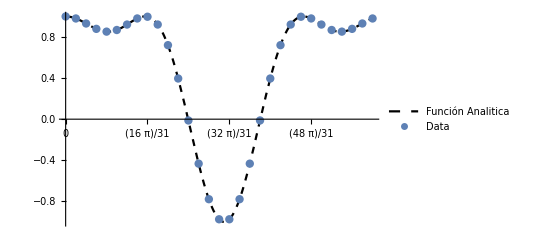

```mathematica
(*Graficando data*)
data=Table[{xval[[j]],yval[[j]]},{j,n}];(*reestructurando lso datos a la forma {Subscript[x, i],Subscript[y, i]}*)

PlotPtos=ListPlot[data,PlotStyle->PointSize[0.015],PlotLegends->{"Data"},AxesLabel->{"θ","f(x)"},Ticks->{xval[[;;;;2]],Automatic}];
PlotFunc=Plot[f[x],{x,xval[[1]],xval[[-1]]},PlotStyle->{Dashed,Black},FrameLabel->{"θ","f(x)"},Ticks->{xval[[;;;;2]],Automatic},PlotLegends->{"Función Analitica"},PlotRange->Automatic];
Show[{PlotFunc,PlotPtos}]
```

Interpolando

```mathematica
(*Forma matricial*)
Mat = matriz[data0]; (*Creando la matriz*)
MatrixForm[Mat];(*Para Visualizar quitar ;*)
```

row: {1/2,Cos[x],Cos[2 x],Cos[3 x],Cos[4 x],Cos[5 x],Cos[6 x],Cos[7 x],Cos[8 x],Cos[9 x],Cos[10 x],Cos[11 x],Cos[12 x],Cos[13 x],Cos[14 x],Cos[15 x],Sin[x],Sin[2 x],Sin[3 x],Sin[4 x],Sin[5 x],Sin[6 x],Sin[7 x],Sin[8 x],Sin[9 x],Sin[10 x],Sin[11 x],Sin[12 x],Sin[13 x],Sin[14 x],Sin[15 x]}

```mathematica
(*Cálculo de las incógnitas*)
InvMatriz=Inverse[Mat];
MatrixForm[InvMatriz]; (*Para Visualizar quitar ;*)

Print["Las incógnitas tienen valor:"]
incog=InvMatriz.yval//Simplify
```

Las incógnitas tienen valor:

{1.,0.75,-0.5,0.25,-1.04083×10^-16,-1.249×10^-16,4.85723×10^-17,1.38778×10^-17,-2.08167×10^-17,6.245×10^-17,-6.93889×10^-17,-1.38778×10^-17,-1.249×10^-16,-6.93889×10^-18,-6.93889×10^-17,9.02056×10^-17,-1.04083×10^-16,9.36751×10^-17,-8.32667×10^-17,1.38778×10^-17,5.55112×10^-17,-2.08167×10^-17,-2.08167×10^-17,-1.38778×10^-17,-3.46945×10^-17,0.,1.38778×10^-17,2.77556×10^-16,-5.55112×10^-17,-1.11022×10^-16,5.55112×10^-17}

```mathematica
incogAnalit=N@Incognitas[data0]
```

{1.,0.75,-0.5,0.25,0.,-7.16273×10^-18,5.73018×10^-17,5.73018×10^-17,-1.43255×10^-17,5.73018×10^-17,-5.73018×10^-17,0.,-2.14882×10^-17,-7.16273×10^-17,7.16273×10^-18,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

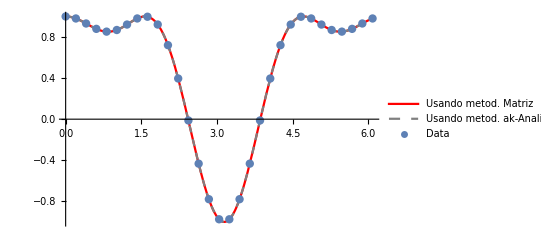

```mathematica
(*Graficando*)
PlotInterpM=Plot[Pf[x,incog],{x,xval[[1]],xval[[-1]]},PlotStyle->Red,PlotLegends->{"Usando metod. Matriz"}, PlotRange->All];
PlotInterp=Plot[Pf[x,incogAnalit],{x,xval[[1]],xval[[-1]]},PlotStyle->{Dashed,Gray},PlotLegends->{"Usando metod. ak-Analitico"}];
Show[{PlotInterpM,PlotInterp, PlotPtos}]
```

### Preguntas:

Pruebe usando f[x_]:=Sin[x]^2+x*Cos[x]* como función de prueba. Explique el resultado obtenido. ¿Por qué no pasan por los datos las funciones interpoladas?

Varie el número de datos y vea cuán bien ajusta.

Compare los resultados obtenidos para las incógnitas por la via matricial y analítica. ¿Qué concluye?